```mathematica
fr[θ_]:=v(Cos[θ]+Sin[θ])

ft[θ_]:=v(Cos[θ]-Sin[θ])
```

```mathematica
FullSimplify[Solve[-R Sin[θ[t]] θ1[t]==v-fr[θ[t]]Cos[θ[t]],θ1[t]]]
```

{{θ1[t]→(v (Cos[θ[t]]-Sin[θ[t]]))/R}}

```mathematica
Clear[θ]
"FullSimplify[DSolve[{θ[0]==0,θ'[t]==(v (Cos[θ[t]] - Sin[θ[t]]))/R},θ[t],t]]"
"evol f appr"
Normal[Series[(v (Cos[θ[t]]-Sin[θ[t]]))/R,{θ[t],π/4,3}]]
"expanded force r"
Normal[Series[fr[θ],{θ,π/4,1}]]
FullSimplify[DSolve[{θ[0]==0,θ'[t]==-(√2 v (-π/4+θ[t]))/R+(v (-π/4+θ[t])^3)/(3 √2 R)},θ[t],t]]
fra[θ_]:=v+v θ
"here"
Integrate[fra[1-ⅇ^(-(t v)/R)]/τ,{t,0,τ}]
```

FullSimplify[DSolve[{θ[0]==0,θ'[t]==(v (Cos[θ[t]] - Sin[θ[t]]))/R},θ[t],t]]

evol f appr

-(√2 v (-π/4+θ[t]))/R+(v (-π/4+θ[t])^3)/(3 √2 R)

expanded force r

√2 v

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{θ[t]→(-π^3+ⅇ^((2 √2 t v)/R) π (-96+π^2)+4 π √(6 π^2-6 ⅇ^((2 √2 t v)/R) (-96+π^2)))/(-4 π^2+4 ⅇ^((2 √2 t v)/R) (-96+π^2))},{θ[t]→(-π^3+ⅇ^((2 √2 t v)/R) π (-96+π^2)+4 π √(6 π^2-6 ⅇ^((2 √2 t v)/R) (-96+π^2)))/(-4 π^2+4 ⅇ^((2 √2 t v)/R) (-96+π^2))}}

here

2 v+((-1+ⅇ^(-(v τ)/R)) R)/τ

```mathematica
FullSimplify[fr[-2 ArcTan[1-√2 Tanh[(t v)/(√2 R)+ArcCoth[√2]]]]]
```

((-1+ⅇ^(-(v τ)/R)) R+2 v τ)/τ

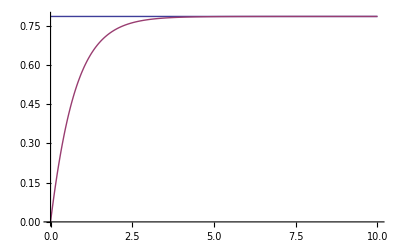

-(R Log[1/(Cosh[(√2 t v)/R]+Sinh[(√2 t v)/R]/(√2))])/τ

v (Cos[a]+Sin[a])

```mathematica
θ[t_]:=-2 ArcTan[1-√2 Tanh[(t v)/(√2 R)+ArcCoth[√2]]]

Plot[{π/4,θ[t]/.{v->1,R->1}},{t,0,10},PlotRange->All]


FullSimplify[τ^-1 Integrate[fr[θ[t]],t]]
fr[a]
```

```mathematica
Simplify[R Log[Cosh[(√2 t v)/R]+Sinh[(√2 t v)/R]/(√2)]/.t->τ-R Log[Cosh[(√2 t v)/R]+Sinh[(√2 t v)/R]/(√2)]/.t->0]
```

R Log[Cosh[(√2 v τ)/R]+Sinh[(√2 v τ)/R]/(√2)]

```mathematica
ftt[t_]:=-R Log[1/(Cosh[(√2 t v)/R]+Sinh[(√2 t v)/R]/(√2))]

FullSimplify[ftt[τ]-ftt[0]]
```

```mathematica
Limit[v R/λ Log[Cosh[(√2 λ)/R]+Sinh[(√2 λ)/R]/(√2)],λ->0,Assumptions->{R>0,v>0,τ>0}]
```

v

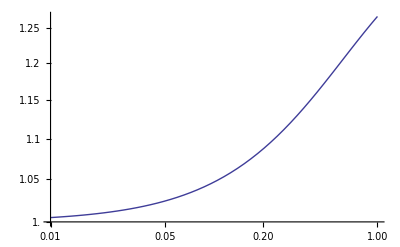

```mathematica
LogLogPlot[R/λ Log[Cosh[(√2 λ)/R]+Sinh[(√2 λ)/R]/(√2)]/.{R->1},{λ,0.01,1}]
```

```mathematica
FullSimplify[(√(Da τ)(R+τ √(Da/τ)fc)√(Da/τ)fc)/R,Assumptions->{Da>0,τ>0,R>0}]
```

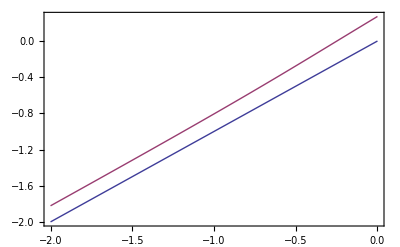

0.156326

```mathematica
fcc[λ_]:=R/λ Log[Cosh[(√2 λ)/R]+Sinh[(√2 λ)/R]/(√2)]

p[λ_]:=(fcc[λ] (R+fcc[λ] λ))/R
p0[λ_]:=(R+ λ)/R

Plot[{Log10[(p0[10^λ]-1.)]/.R->1,Log10[(p[10^λ]-1.)]/.R->1},{λ,-2,0},Frame->True,PlotRange->All,Axes->False]


(p[0.1]-1)/.R->1.
```

```mathematica
Limit[R/λ Log[Cosh[(√2 λ)/R]+Sinh[(√2 λ)/R]/(√2)],λ->0,Assumptions->R>0]
```

1

```mathematica
Limit[R/λ Log[Cosh[(√2 λ)/R]+Sinh[(√2 λ)/R]/(√2)],R->∞,Assumptions->λ>0]
```

1

```mathematica
Series[(-1+ⅇ^(-(v τ)/R)) R+2 v τ,{τ,0,1}]
```

v τ+O[τ]^2

```mathematica
Limit[((-1+ⅇ^(-(v τ)/R)) R+2 v τ)/τ,τ->0]
Limit[((-1+ⅇ^(-(v τ)/R)) R+2 v τ)/τ,τ->∞,Assumptions->{R>0,v>0}]
```

v

2 v

```mathematica
θ[t_]:=-2 ArcTan[1-√2 Tanh[(t v)/(√2 R)+ArcCoth[√2]]]
Integrate[Exp[-v^2](R Log[Cosh[(√2 v τ)/R]+Sinh[(√2 v τ)/R]/(√2)]),{v,0,∞},Assumptions->{R>0,τ>0}]
```

$Aborted

```mathematica
Integrate[Exp[-v^2]Log[Cosh[v]+Sinh[v]/√2],{v,-∞,∞}]
```

Infinity::indet: Indeterminate expression -∞ + ∞ encountered.

∫_(-∞)^∞ ⅇ^(-v^2) Log[Cosh[v]+Sinh[v]/(√2)]ⅆv